# Teaching Game Theory to Kids and Limits of Prediction

Alexander V. Outkin, Jun. 29,  2018

I have once been asked to read a lecture to a group of 6th graders on Game Theory. After agreeing to it, I realized that explaining the game theory basics to 6th graders my be difficult, given that terms such as Nash equilibrium, minimax, maximin, optimization may not resonate in a 6th grade classroom.  Instead I’ve introduced game theory using the rock-paper-scissors (RPS) game. Turns out kids are excellent game-theoreticians.  In RPS, they understood both the benefits of  randomizing their own strategy and of predicting their opponent’s moves. They offered a number of heuristics both for the prediction and opening move.  These heuristics included optimizing against past opponent moves, such as not playing rock if the opponent just played scissors, and playing a specific opening hand, such as “paper”. Visualizing the effects of such strategic choices on-the-fly would be interesting and educational. This brief essay attempts demonstrating and visualizing the value of a few different strategic options in RPS.

Specifically, we would like to illustrate the following: 1) what is the value of being unpredictable?; and 2) what is the value of being able to predict your opponent?

In regard to prediction of human players, the question 2) has been reflected in Jon McLoone's entry in Wolfram Blog from January 20, 2014[1]. McLoone created a predictive algorithm for playing against human opponents, that learns to beat human opponents reliably after approximately 30 - 40 games. I use McLoone's implementation to represent a predictive and random strategies.

The rest of this documents 1) investigates performance of this predictive strategy against a random strategy (which is optimal in RPS) and in 2)  attempts to turn this  predictive power against the predictive strategy by allowing the opponent the full knowledge of the predictor’s strategy (but not the choices made using the strategy). This exposes a weakness in  predictions made without taking risks into account by illustrating that predictive strategy may make  the predictor predictable as well.

## The Rock, Paper, Scissors Game

The game  includes the following components:

Player strategies. Strategy takes the current state and past history and determines new action. It can be represented as a map from history up to the current state to action (Rock, Paper, of Scissors). We represent  R, P, S respectively as 1, 2, 3.

Game history. This includes the actions of both players. Game history at time t is a tuple of both player actions.

Game play outcome at each time.  The game at each time step results in one of the players winning or in a draw. The draw only occurs if both players choose the same action. A graph representing the game outcomes is represented below. Directed links means that origin node beats the sink node. For example P (paper) beats R (rock).

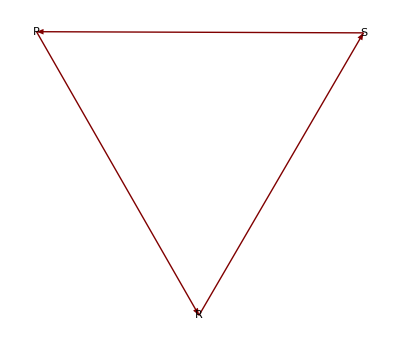

```mathematica
GraphPlot[{R->S,S->P,P->R}, DirectedEdges->True, VertexLabeling->True]
```

Because of the circular nature in the graph above, RPS does not have a Nash equilibrium in pure (deterministic) strategies. The Nash equilibrium strategy for each player to uniformly randomize over the three action choices. We call this strategy “random”.

## Predictive and Random Strategy Implementation

I start with predictive strategy from [1]. I changed it to look back to the past 100 games, rather than to the entire history, to speed-up the code.

```mathematica
Code (* Predictive and Random Strategies Implementation*)
```

```mathematica
(* Probabilistic prediction based on past choices of player 2 *)
prediction[pastChoices_List]:={If[Length[pastChoices]<2,1,DistributionFitTest[pastChoices,DiscreteUniformDistribution[{1,3}]]],
					RandomChoice[Commonest[pastChoices/.{}->{1,2,3}]]};
(* Search throught patters of historic play *)
historySeek[history_,n_Integer,col_]:=If[n>Length[history]-1,{},
If[#==={},{},#[[1,All,1]]]&[
Reap[Do[
If[history[[i;;(i+n-1),col]]===history[[-n;;,col]],Sow[history[[i+n]]]],
{i,Length[history]-n}]][[2]]]];
(* Wrappers for prediction *)
bestGuess[{}]:=RandomInteger[{1,3}];
bestGuess[data_]:=Block[{max=Min[100, Length[data]]},
Sort[Flatten[Outer[prediction[historySeek[data,#1,#2]]&,Range[max],{1,2,All}],{1,2}]]][[1,-1]];

chooseGo[data_]:=Mod[bestGuess[data]+1,3,1];
(* Utility to calculate historic game outcomes based on historic play *)
winTest[p1_,p2_]:=Switch[Mod[p1-p2,3],
				0,"Draw",
				1,"Win",
				2,"Lose"];
```

## 1. Prediction vs. Randomization

This experiment shows the cumulative payoff of the predictive strategy against  random strategy for a game of 1000 moves.

```mathematica
history2 = {{1, 1}}
Nest[AppendTo[history2, {chooseGo[#], chooseGo[{}]}]&,history2,1000];
```

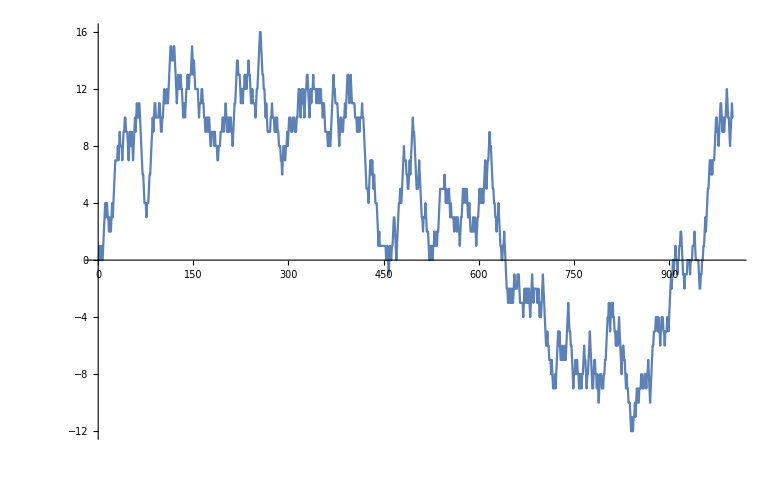

```mathematica
outcomes2 = (winTest@@@history2)/.{"Win"->1,"Lose"->-1,"Draw"->0};
ListLinePlot[Accumulate[outcomes2]]
```

The cumulative payoff of the predictive strategy spends most of the time in positive domain. It is not entirely expected, because it is playing against the optimal strategy in RPS for which there is nothing to predict. This may be a consequence of the predictive strategy being probabilistic and thus randomizing in response to a random strategy.

## 2. Random vs. Random

This experiment shows the cumulative payoff of the optimal strategy (random) playing against the same strategy.

```mathematica
history3 = {{1, 1}}
Nest[AppendTo[history3, {chooseGo[{}], chooseGo[{}]}]&,history3,1000];
```

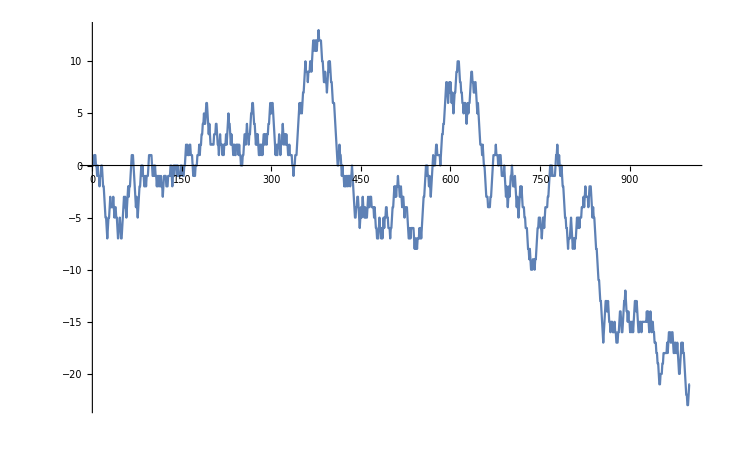

```mathematica
outcomes3 = (winTest@@@history3)/.{"Win"->1,"Lose"->-1,"Draw"->0};
ListLinePlot[Accumulate[outcomes3]]
```

There is no clear winner in two random optimal strategies playing against each other, which is expected. The probabily of deviations of the cumulative payoff from zero can be evaluated analytically.

## 3. Beating the Predictor at their Own Game

Here we assume that the first player is using the same probabilistic strategy as before, but the second player has access to the first player strategy definition, but not the choices made by the strategy, and are using a naive probabilistic optimization against the first player strategy.

```mathematica
Code (* This desribes the player 2 strategy that exploits predictability inherent in the predictive strategy *)
```

```mathematica
antiPrediction[pastChoices_List]:={If[Length[pastChoices]<2,1,DistributionFitTest[pastChoices,DiscreteUniformDistribution[{1,3}]]],
					RandomChoice[Commonest[pastChoices/.{}->{1,2,3}]]};

worstGuess[{}]:=RandomInteger[{1,3}];
worstGuess[data_]:=Block[{max=Min[100, Length[data]]},
Sort[Flatten[Outer[antiPrediction[historySeek[data,#1,#2]]&,Range[max],{1,2,All}],{1,2}]]][[1,-1]];
antiChooseGo[data_]:=Mod[worstGuess[data]+1,3,1];
```

```mathematica
history4 = {{1, 1}}
Nest[AppendTo[history4, {chooseGo[#], antiChooseGo[#]}]&,history4,1000];
```

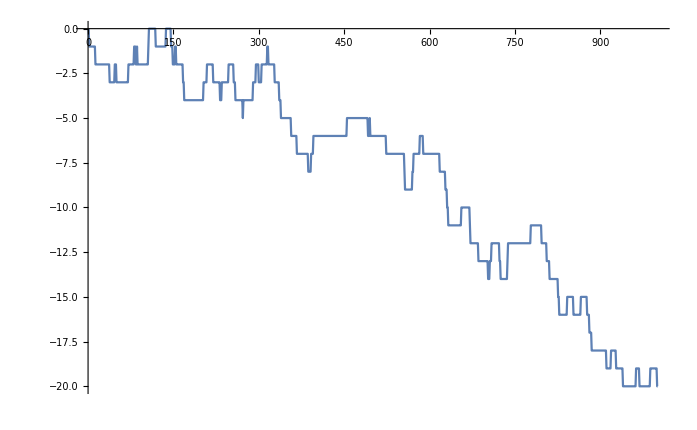

```mathematica
outcomes4 = (winTest@@@history4)/.{"Win"->1,"Lose"->-1,"Draw"->0};
ListLinePlot[Accumulate[outcomes4]]
```

This shows the predictive strategy cumulative payoff convincingly trending down over the course of 1000 games and indicates limits of prediction in the face of better predictive capabilities. However, it is unclear why the predictive strategy of the first player does not converge to a random play as may have happened against random strategy.

## Further explorations

While extremely simple and incomplete, these examples may have bearing on the following topics:

Limits of prediction
Predictive strategy is reasonably effective against the optimal (in the Nash equilibrium sense)  strategy.
The specific predictive strategy used here is ineffective against generally suboptimal strategy that has access to the predictive strategy decision rule.
These two observations imply that predictive strategies should be used with caution.

Application to automated decision making in society
The result in experiment 3. maybe indicative of potential problems with self-driving cars and other autonomous technologies. For example if the autonomous cars attempt to optimise on their local objective, they may (inadvertently) exploit weakness in predictive strategies of other autonomous cars leading to globally sub-optimal outcomes.

Kids appear to be enthusiastic and skilled RPS players. Yet, you rarely see grown-ups playing RPG, who seem to prefer throwing a coin or a dice or doing some other kind of randomization that requires no skill or predictive ability. Is it because kids are optimistic about their ability to predict the future? To affect it? Do adults optimize and conserve the resources by not bothering with prediction in certain situations?

## References

[1] http://demonstrations.wolfram.com/RockPaperScissorsWithAIPlayer/

## Acknowledgements

I would like to thank Matthew Szudzik for valuable suggestions and comments and Vladimir Grankovsky, Jonathan Gorard and other WSS2018 participants for help with Wolfram language and Mathematica.

## Author contact information

avoutki@sandia.gov

Sandia National Laboratories

Sandia National Laboratories is a multimission laboratory managed and operated by National Technology and Engineering Solutions of Sandia, LLC, a wholly owned subsidiary of Honeywell International, Inc., for the U.S. Department of Energy’s National Nuclear Security Administration under contract DE-NA-0003525.